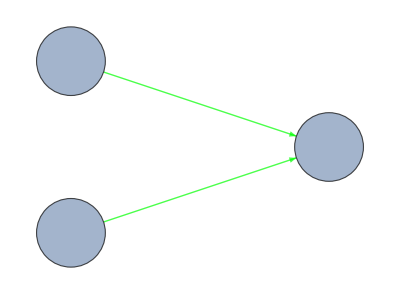

```mathematica
Graph[{"A"->"C","B"->"C"}, 
ertexCoordinates->{"A"->{0,0},"B"->{0,2},"C"->{3,1}},VertexLabels->Placed[Automatic,Center],VertexSize->0.4,EdgeStyle->{"A"->"C"->RGBColor[0, 1, 0],"B"->"C"->RGBColor[0, 1, 0],Thickness[Large]}]
```

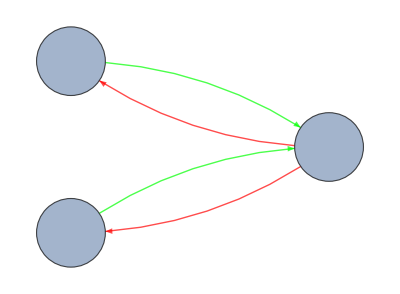

```mathematica
Graph[{"A"->"C","B"->"C", "C"->"A", "C"->"B"}, 
VertexCoordinates->{"A"->{0,0},"B"->{0,2},"C"->{3,1}},VertexLabels->Placed[Automatic,Center],VertexSize->0.4,EdgeStyle->{"A"->"C"->RGBColor[0, 1, 0],"B"->"C"->RGBColor[0, 1, 0],"C"->"A"->Red,"C"->"B"->Red,Thickness[Large]}]
```

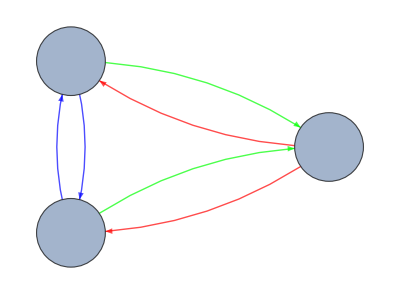

```mathematica
Graph[{"A"->"C","B"->"C", "C"->"A", "C"->"B", "A"->"B","B"->"A"}, 
VertexCoordinates->{"A"->{0,0},"B"->{0,2},"C"->{3,1}},VertexLabels->Placed[Automatic,Center],VertexSize->0.4,EdgeStyle->{"A"->"C"->RGBColor[0, 1, 0],"B"->"C"->RGBColor[0, 1, 0],
"C"->"A"->Red,"C"->"B"->Red,
"A"->"B"->Blue,"B"->"A"->Blue, Thickness[Large]}]
```

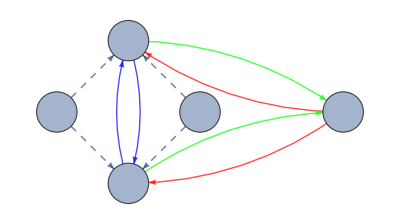

```mathematica
Graph[{"A"->"C","B"->"C", "C"->"A", "C"->"B", "A"->"B","B"->"A",
"(A; B)"->"A", "(A; B)"->"B",
"(B; A)"->"A", "(B; A)"->"B"}, 
VertexCoordinates->{"A"->{0,0},"B"->{0,2},"C"->{3,1}, "(A; B)"->{-1, 1},"(B; A)"->{1,1}},VertexLabels->Placed[Automatic,Center],VertexSize->0.4,EdgeStyle->{"A"->"C"->RGBColor[0, 1, 0],"B"->"C"->RGBColor[0, 1, 0],
"C"->"A"->Red,"C"->"B"->Red,
"A"->"B"->Blue,"B"->"A"->Blue,
"(A; B)" ->"B"->Dashed, 
"(A; B)"->"A"-> Dashed,
"(B; A)"->"A"->Dashed,
"(B; A)"->"B"-> Dashed,Thickness[Large]}]
```